## Definitions of Wigners and stuff

```mathematica
Needs["utilities`"];
Needs["GeneralUtilities`"];
ClearAll[klyshko,klyshkoInf];
klyshko[n_Integer]:=(n!P[n])^2-(n-1)!(n+1)!P[n-1]P[n+1];
klyshko[n_Integer,probs_List]:=(n!probs⟦n+1⟧)^2-(n-1)!(n+1)!probs⟦n⟧probs⟦n+2⟧;
klyshkoInf[n_Integer]:=Sum[P[k],{k,0,n-2}]+((n-1)!P[n-1])^n/((n)!P[n])^(n-1)(ⅇ^((n! P[n])/((n-1)!P[n-1]))-Sum[1/(k!)((n!P[n])/((n-1)!P[n-1]))^k,{k,0,n-2}]);
klyshkoInf[n_Integer,probs_List]:=Sum[probs⟦k+1⟧,{k,0,n-2}]+((n-1)!probs⟦n⟧)^n/((n)!probs⟦n+1⟧)^(n-1)(ⅇ^((n! probs⟦n+1⟧)/((n-1)!probs⟦n⟧))-Sum[1/(k!)((n!probs⟦n+1⟧)/((n-1)!probs⟦n⟧))^k,{k,0,n-2}]);
poisson[λ_,n_]:=ⅇ^-λ λ^n/n!;
poisson[λs_List,n_]:=Sum[Exp[-λ] λ^n,{λ,λs}]/n!;


Qprobs[λs_,s_]:=poisson[λs,s]s!

(*SetOptions[Plot,
Frame->True,FrameStyle->Directive[Black,Thick,Large],GridLines->Automatic,PlotStyle->Thickness@0.006,PlotRangePadding->None,ImageSize->500
];*)
```

```mathematica
W0[x_,p_]=1/(2π)ⅇ^(-p^2/2-x^2/2) ;
W1[x_,p_]=(ⅇ^(-p^2/2-x^2/2) (-1+p^2+x^2))/(2 π);
W2[x_,p_]=(ⅇ^(1/2 (-p^2-x^2)) (2+p^4-4 x^2+x^4+2 p^2 (-2+x^2)))/(4 π);
W3[x_,p_]=(ⅇ^(1/2 (-p^2-x^2)) (-6+p^6+18 x^2-9 x^4+x^6+3 p^4 (-3+x^2)+3 p^2 (6-6 x^2+x^4)))/(12 π);
W4[x_,p_]=1/(48 π)ⅇ^(1/2 (-p^2-x^2)) (24+p^8-96 x^2+72 x^4-16 x^6+x^8+4 p^6 (-4+x^2)+6 p^4 (12-8 x^2+x^4)+4 p^2 (-24+x^2 (-6+x^2)^2));
W5[x_,p_]=1/(240 π)ⅇ^(1/2 (-p^2-x^2)) (-120+p^10+5 p^8 (-5+x^2)+10 p^6 (20-10 x^2+x^4)+x^2 (30-15 x^2+x^4) (20-10 x^2+x^4)+10 p^4 (-60+60 x^2-15 x^4+x^6)+5 p^2 (120-240 x^2+120 x^4-20 x^6+x^8));
W6[x_,p_]=1/(1440 π)ⅇ^(1/2 (-p^2-x^2)) (720+p^12+6 p^10 (-6+x^2)+15 p^8 (30-12 x^2+x^4)+20 p^6 (-120+90 x^2-18 x^4+x^6)+x^2 (-6+x^2) (720-780 x^2+270 x^4-30 x^6+x^8)+15 p^4 (360-480 x^2+180 x^4-24 x^6+x^8)+6 p^2 (-720+1800 x^2-1200 x^4+300 x^6-30 x^8+x^10));
W7[x_,p_]=1/(10080 π)ⅇ^(1/2 (-p^2-x^2)) (-5040+p^14+35280 x^2-52920 x^4+29400 x^6-7350 x^8+882 x^10-49 x^12+x^14+7 p^12 (-7+x^2)+21 p^10 (42-14 x^2+x^4)+35 p^8 (-210+126 x^2-21 x^4+x^6)+35 p^6 (840-840 x^2+252 x^4-28 x^6+x^8)+21 p^4 (-2520+4200 x^2-2100 x^4+420 x^6-35 x^8+x^10)+7 p^2 (5040-15120 x^2+12600 x^4-4200 x^6+630 x^8-42 x^10+x^12));
W8[x_,p_]=1/(80640 π)ⅇ^(1/2 (-p^2-x^2)) (40320+p^16-322560 x^2+564480 x^4-376320 x^6+117600 x^8-18816 x^10+1568 x^12-64 x^14+x^16+8 p^14 (-8+x^2)+28 p^12 (56-16 x^2+x^4)+56 p^10 (-336+168 x^2-24 x^4+x^6)+70 p^8 (1680-1344 x^2+336 x^4-32 x^6+x^8)+56 p^6 (-6720+8400 x^2-3360 x^4+560 x^6-40 x^8+x^10)+28 p^4 (20160-40320 x^2+25200 x^4-6720 x^6+840 x^8-48 x^10+x^12)+8 p^2 (-40320+141120 x^2-141120 x^4+58800 x^6-11760 x^8+1176 x^10-56 x^12+x^14));
W9[x_,p_]=1/(725760 π)ⅇ^(1/2 (-p^2-x^2)) (-362880+p^18+3265920 x^2-6531840 x^4+5080320 x^6-1905120 x^8+381024 x^10-42336 x^12+2592 x^14-81 x^16+x^18+9 p^16 (-9+x^2)+36 p^14 (72-18 x^2+x^4)+84 p^12 (-504+216 x^2-27 x^4+x^6)+126 p^10 (3024-2016 x^2+432 x^4-36 x^6+x^8)+126 p^8 (-15120+15120 x^2-5040 x^4+720 x^6-45 x^8+x^10)+84 p^6 (60480-90720 x^2+45360 x^4-10080 x^6+1080 x^8-54 x^10+x^12)+36 p^4 (-181440+423360 x^2-317520 x^4+105840 x^6-17640 x^8+1512 x^10-63 x^12+x^14)+9 p^2 (362880-1451520 x^2+1693440 x^4-846720 x^6+211680 x^8-28224 x^10+2016 x^12-72 x^14+x^16));
W10[x_,p_]=1/(7257600 π)ⅇ^(1/2 (-p^2-x^2)) (3628800+p^20-36288000 x^2+81648000 x^4-72576000 x^6+31752000 x^8-7620480 x^10+1058400 x^12-86400 x^14+4050 x^16-100 x^18+x^20+10 p^18 (-10+x^2)+45 p^16 (90-20 x^2+x^4)+120 p^14 (-720+270 x^2-30 x^4+x^6)+210 p^12 (5040-2880 x^2+540 x^4-40 x^6+x^8)+252 p^10 (-30240+25200 x^2-7200 x^4+900 x^6-50 x^8+x^10)+210 p^8 (151200-181440 x^2+75600 x^4-14400 x^6+1350 x^8-60 x^10+x^12)+120 p^6 (-604800+1058400 x^2-635040 x^4+176400 x^6-25200 x^8+1890 x^10-70 x^12+x^14)+45 p^4 (1814400-4838400 x^2+4233600 x^4-1693440 x^6+352800 x^8-40320 x^10+2520 x^12-80 x^14+x^16)+10 p^2 (-3628800+16329600 x^2-21772800 x^4+12700800 x^6-3810240 x^8+635040 x^10-60480 x^12+3240 x^14-90 x^16+x^18));
wignerK[k_Integer]:={W0,W1,W2,W3,W4,W5,W6,W7,W8,W9,W10}⟦k+1⟧;
wignerTildeK[k_Integer,α_]:=Function[{x,p},wignerK[k][x+Re@α,p+Im@α]];
```

```mathematica
{4π Integrate[ W0[x,p]^2,{x,-Infinity,Infinity},{p,-Infinity,Infinity}],
4π Integrate[ W1[x,p]^2,{x,-Infinity,Infinity},{p,-Infinity,Infinity}],
4π Integrate[ W0[x,p]W1[x,p],{x,-Infinity,Infinity},{p,-Infinity,Infinity}]}
```

{1,1,0}

```mathematica
{wignerK[0][x,p],wignerK[1][x,p]}
```

{(ⅇ^(-p^2/2-x^2/2))/(2 π),(ⅇ^(-p^2/2-x^2/2) (-1+p^2+x^2))/(2 π)}

## Displaced coherent states

```mathematica
displacedCoherent1P0=4π Integrate[
wignerK[0][x,p]wignerTildeK[1,α][x,p],
{x,-Infinity,Infinity},{p,-Infinity,Infinity}
]/.{α->Sqrt@μ ⅇ^(I ϕ)}/.{μ->4μ}//FullSimplify[#,{μ,ϕ}∈Reals&&μ≥0]&
```

ⅇ^-μ μ

```mathematica
displacedCoherent1P1=4π Integrate[
wignerK[1][x,p]wignerTildeK[1,α][x,p],
{x,-Infinity,Infinity},{p,-Infinity,Infinity}
]/.{α->Sqrt@μ ⅇ^(I ϕ)}/.{μ->4μ}//FullSimplify[#,{μ,ϕ}∈Reals&&μ≥0]&
```

ⅇ^-μ (-1+μ)^2

```mathematica
displacedCoherent1P2=4π Integrate[
wignerK[2][x,p]wignerTildeK[1,α][x,p],
{x,-Infinity,Infinity},{p,-Infinity,Infinity}
]/.{α->Sqrt@μ ⅇ^(I ϕ)}/.{μ->4μ}//FullSimplify[#,{μ,ϕ}∈Reals&&μ≥0]&
```

1/2 ⅇ^-μ (-2+μ)^2 μ

```mathematica
ClearAll@displacedCoherent1Ps;
displacedCoherent1Ps[μ_]:={ⅇ^-μ μ,ⅇ^-μ (-1+μ)^2,1/2 ⅇ^-μ (-2+μ)^2 μ};
displacedFockProbs[n_,μ_,ks_List]:=displacedFockProbs[n,μ,#]&/@ks;
displacedFockProbs[n_,μ_,k_]:=(k!)/(n!)μ^(k-n)ⅇ^-μ Sum[Binomial[n,j](-μ)^j/(k-n+j)!,{j,Min[0,n-k],n}]^2
```

```mathematica
ClearAll@klyshkoExpr
```

```mathematica
klyshko1Expr[α2_]=ReplaceAll[klyshko[1],
{P[0]->4π  prob0Simplified,P[1]->4π  prob1Simplified,P[2]->4π  prob2Simplified}
]//FullSimplify//Collect[#,α2,Simplify]&;
klyshkoInfExpr[α2_]=ReplaceAll[klyshkoInf[2],
{P[0]->4π  prob0Simplified,P[1]->4π  prob1Simplified,P[2]->4π  prob2Simplified}
]//FullSimplify//Collect[#,α2,Simplify]&;
```

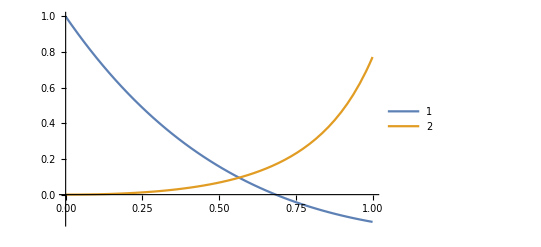

```mathematica
Plot[{klyshko1Expr[λ],klyshkoInfExpr[λ]-1},{λ,0,1},PlotRange->All,PlotLegends->Automatic]
```

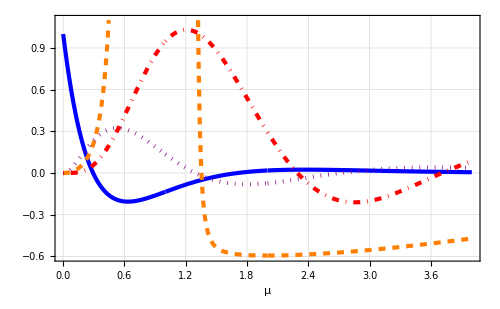

```mathematica
fig=Plot[
{klyshko[1],klyshkoInf[2]-1,klyshko[2],klyshko[3]}/.Thread@Rule[{P[0],P[1],P[2],P[3],P[4]},displacedFockProbs[1,μ,{0,1,2,3,4}]]//Evaluate,
{μ,0,4},PlotRange->{All,{-0.6,1.1}},Exclusions->{1,2},Frame->True,FrameTicks->True,FrameStyle->Directive[Black,Thick,Large],GridLines->Automatic,PlotStyle->{Directive[Blue,Thickness@0.006],Directive[Orange,Thickness@0.006,Dashed],Directive[Purple,Thickness@0.006,Dotted],Directive[Red,Thickness@0.006,DotDashed]},FrameLabel->{"μ"},PlotRangePadding->None,ImageSize->500,Axes->True]
```

```mathematica
Export[FileNameJoin@{"/home/lk/Documents/docs/research/Radim/draft/figures","Ki_displacedFock1_vs_mu.pdf"},fig]
```

/home/lk/Documents/docs/research/Radim/draft/figures/Ki_displacedFock1_vs_mu.pdf

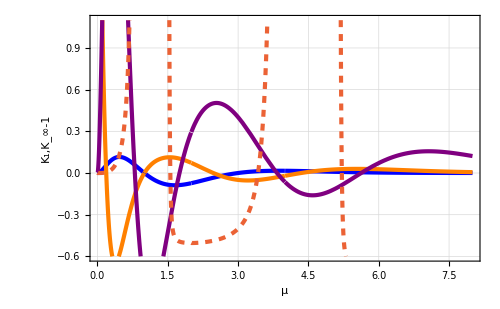

```mathematica
Plot[
{klyshko[1],klyshko[2],klyshko[3],klyshkoInf[4]-1}/.Thread@Rule[{P[0],P[1],P[2],P[3],P[4]},displacedFockProbs[2,μ,{0,1,2,3,4}]]//Simplify//Evaluate,
{μ,0,8},PlotRange->{All,{-0.6,1.1}},Exclusions->{1,2,4},PlotStyle->{Directive[Thickness@0.006,Blue],Directive[Thickness@0.006,Orange],Directive[Thickness@0.006,Purple],Directive[Thickness@0.006,Dashed]},FrameLabel->{"μ","K_1,K_∞-1"}]
```

### Check that these states cross a region in which the original Klyshko does not detect nonclassicality

```mathematica
Show[ContourPlot3D[
{p1^2-2p0 p2==0
,p0+((-1+ⅇ^((2 p2)/p1)) p1^2)/(2 p2)==1},
{p0,0,0.5},{p1,0.001,1},{p2,0,.6},PlotRange->{{0,0.5},{0,1},{0,0.4}},AxesLabel->{"P_0","P_1","P_2"},ContourStyle->Opacity[0.5],AxesStyle->Directive[Black,Thick,Large],BoxStyle->Directive[Black,Thick],MaxRecursion->2,PlotPoints->30],
ParametricPlot3D[ⅇ^-λ λ^{0,1,2}/{0,1,2}!,{λ,0,20},PlotStyle->{Black}]
,ParametricPlot3D[displacedCoherent1Ps[λ],{λ,0,1-1/Sqrt@2.},PlotStyle->{Thickness@0.01,Red}]
,ParametricPlot3D[displacedCoherent1Ps[λ],{λ,1-1/Sqrt@2.,1.35},PlotStyle->{Thickness@0.01,Purple}]
,ParametricPlot3D[displacedCoherent1Ps[λ],{λ,1.35,1+1/Sqrt@2.},PlotStyle->{Thickness@0.01,Darker@Green}]
,ParametricPlot3D[displacedCoherent1Ps[λ],{λ,1+1/Sqrt@2.,10},PlotStyle->{Thickness@0.01,Red}]
]
```

-Graphics3D-

```mathematica
Show[ContourPlot3D[
{p1^2-2p0 p2==0
,p0+((-1+ⅇ^((2 p2)/p1)) p1^2)/(2 p2)==1},
{p0,0,0.1},{p1,0.0001,0.1},{p2,0,.1},PlotRange->{{0,0.1},{0,.1},{0,0.1}},AxesLabel->{"P_0","P_1","P_2"},ContourStyle->Opacity[0.5],AxesStyle->Directive[Black,Thick,Large],BoxStyle->Directive[Black,Thick],MaxRecursion->2,PlotPoints->30],
ParametricPlot3D[ⅇ^-λ λ^{0,1,2}/{0,1,2}!,{λ,0,20},PlotStyle->{Black}]
,ParametricPlot3D[displacedCoherent1Ps[λ],{λ,1+1/Sqrt@2.,12},PlotStyle->{Thickness@0.01,Red}]
]
```

-Graphics3D-

```mathematica
exportHere["coolfig.pdf",fig]
```

/home/lk/Downloads/coolfig.pdf

```mathematica
SystemOpen[NotebookDirectory[]]
```

```mathematica
Integrate[x^2 Exp[-x^2],{x,0,Infinity}]
```

(√π)/4

```mathematica
With[{μ=0,σ=1},
PDF[NormalDistribution[μ,σ],x]displacedCoherent1[λ]⟦1⟧
```

(ⅇ^(-λ/4-(x-μ)^2/(2 σ^2)) (-8+λ)^2 λ)/(128 √(2 π) σ)

```mathematica
Integrate[
PDF[NormalDistribution[μ,σ],x]#,{λ,-Infinity,Infinity}
]&/@displacedCoherent1[λ]
```

Integrate::idiv: Integral of (ⅇ^(-λ/4-(((«1»«1»)^2)/(2 σ^2)) (-8+λ)^2 λ)/(128 √(2 π) σ) does not converge on {-∞,∞}.

Integrate::idiv: Integral of (ⅇ^(-λ/4-(((«1»«1»)^2)/(2 σ^2)) (32+(-16+λ) λ)^2)/(1024 √(2 π) σ) does not converge on {-∞,∞}.

Integrate::idiv: Integral of (ⅇ^(-λ/4-(((«1»«1»)^2)/(2 σ^2)) λ (96+(-24+λ) λ)^2)/(12288 √(2 π) σ) does not converge on {-∞,∞}.

General::stop: Further output of Integrate::idiv will be suppressed during this calculation.

{∫_(-∞)^∞ (ⅇ^(-λ/4-(x-μ)^2/(2 σ^2)) (-8+λ)^2 λ)/(128 √(2 π) σ)ⅆλ,∫_(-∞)^∞ (ⅇ^(-λ/4-(x-μ)^2/(2 σ^2)) (32+(-16+λ) λ)^2)/(1024 √(2 π) σ)ⅆλ,∫_(-∞)^∞ (ⅇ^(-λ/4-(x-μ)^2/(2 σ^2)) λ (96+(-24+λ) λ)^2)/(12288 √(2 π) σ)ⅆλ}

```mathematica
displacedCoherent1[λ]
```

{1/128 ⅇ^(-λ/4) (-8+λ)^2 λ,(ⅇ^(-λ/4) (32+(-16+λ) λ)^2)/1024,(ⅇ^(-λ/4) λ (96+(-24+λ) λ)^2)/12288}

```mathematica
displacedCoherent1[α1^2+α2^2]//Simplify
```

{1/128 ⅇ^(-α1^2/4-α2^2/4) (-8+α1^2+α2^2)^2 (α1^2+α2^2),(ⅇ^(-α1^2/4-α2^2/4) (32+(-16+α1^2+α2^2) (α1^2+α2^2))^2)/1024,(ⅇ^(-α1^2/4-α2^2/4) (α1^2+α2^2) (96+(-24+α1^2+α2^2) (α1^2+α2^2))^2)/12288}

Define formulae for arbitrary displaced Fock states (effectively, the MEL of the displacement operator)

```mathematica
displacedCoherentMELs[μ_,k_,ell_]:=ⅇ^-μ μ^(k-ell)Sum[
(-1)^n μ^n/(n!)√FactorialPower[ell,n] FactorialPower[k,ell-n] 1/(√(k!(ell-n)!)),
{n,0,ell}]^2;
```

```mathematica
displacedCoherentMELs[μ,k,0]//Simplify
```

(ⅇ^-μ μ^k)/(k!)

```mathematica
displacedCoherentMELs[μ,k,1]//Simplify
```

(ⅇ^-μ (k-μ)^2 μ^(-1+k))/(k!)

```mathematica
displacedCoherentMELs[μ,k,2]//FullSimplify[#,k∈Integers]&
```

(ⅇ^-μ μ^(-2+k) (μ (-2 k+μ)+FactorialPower[k,2])^2)/(2 k!)

```mathematica
displacedCoherentMELs[μ,{0,1,2},2]//FullSimplify
```

{1/2 ⅇ^-μ μ^2,1/2 ⅇ^-μ (-2+μ)^2 μ,1/4 ⅇ^-μ (2+(-4+μ) μ)^2}

```mathematica
Show[ContourPlot3D[
{p1^2-2p0 p2==0
,p0+((-1+ⅇ^((2 p2)/p1)) p1^2)/(2 p2)==1},
{p0,0,0.5},{p1,0.001,1},{p2,0,1},PlotRange->{{0,0.5},{0,1},{0,1}},AxesLabel->{"P_0","P_1","P_2"},ContourStyle->Opacity[0.5],AxesStyle->Directive[Black,Thick,Large],BoxStyle->Directive[Black,Thick],MaxRecursion->2,PlotPoints->30],
ParametricPlot3D[ⅇ^-λ λ^{0,1,2}/{0,1,2}!,{λ,0,20},PlotStyle->{Black}]
,ParametricPlot3D[displacedCoherentMELs[μ,{0,1,2},2]//FullSimplify//Evaluate,{μ,0,12},PlotStyle->{Thickness@0.01,Red}]
]
```

-Graphics3D-

## Thermal averaged displaced Focks

Distributions of displaced Fock states, check normalization and average are what they should

```mathematica
{Sum[ⅇ^-μ μ^(k-1)/(k!)(μ-k)^2,{k,0,Infinity}],Sum[k ⅇ^-μ μ^(k-1)/(k!)(μ-k)^2,{k,0,Infinity}]//Simplify}
```

{1,1+μ}

Compute the thermal average over the above requires to compute the following integral:

```mathematica
Integrate[1/n ⅇ^(-μ/n)(ⅇ^-μ μ^(k-1))/(k!)(μ-k)^2,{μ,0,Infinity}]
```

ConditionalExpression[((1+1/n)^-k (k+n^2) Gamma[1+k])/(n (1+n)^2 k!),Re[k]>0&&Re[1/n]>-1]

```mathematica
1/(c^(k+2)μ)(c(c-2)k+k+1)/.{c->1+1/μ}//FullSimplify[#,k∈Integers&&k>0]&
```

((1+1/μ)^-k (k+μ^2))/(μ (1+μ)^2)

```mathematica
thermalAveragedProb[k_,n_]=1/(n c^(k+2))(k+1-2c k+c^2 k)/.{c->1+1/n}//FullSimplify
```

((1+1/n)^-k (k+n^2))/(n (1+n)^2)

```mathematica
displacedFockProbs[1,μ,0]
```

ⅇ^-μ μ

Consistency check: normalization and average of thermally averaged probability

```mathematica
{Sum[thermalAveragedProb[k,n],{k,0,Infinity}],
Sum[k thermalAveragedProb[k,n],{k,0,Infinity}]}
```

{1,1+n}

```mathematica
thermalAveragedProb[{0,1,2},n]//FullSimplify
```

{n/(1+n)^2,(1+n^2)/(1+n)^3,(n (2+n^2))/(1+n)^4}

```mathematica
klyshko[1,thermalAveragedProb[{0,1,2},n]]//FullSimplify
```

-(-1+2 n^2+n^4)/(1+n)^6

```mathematica
N@Solve[-1+2 x+x^2==0,x]
```

{{x→-2.41421},{x→0.414214}}

```mathematica
-1+Sqrt@2.
```

0.414214

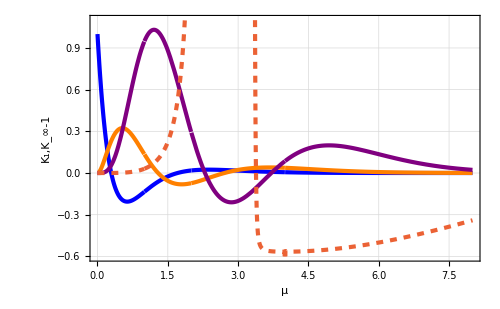

```mathematica
Plot[
{klyshko[1],klyshko[2],klyshko[3],klyshkoInf[4]-1}/.Thread@Rule[{P[0],P[1],P[2],P[3],P[4]},displacedFockProbs[1,μ,{0,1,2,3,4}]]//Simplify//Evaluate,
{μ,0,8},PlotRange->{All,{-0.6,1.1}},Exclusions->{1,2,4},PlotStyle->{Directive[Thickness@0.006,Blue],Directive[Thickness@0.006,Orange],Directive[Thickness@0.006,Purple],Directive[Thickness@0.006,Dashed]},FrameLabel->{"μ","K_1,K_∞-1"}]
```

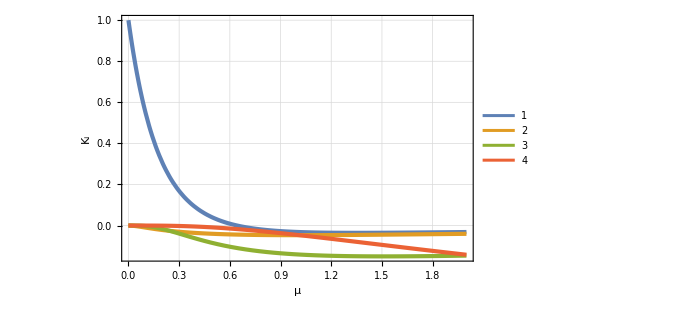

```mathematica
Plot[{klyshko[1],klyshko[2],klyshko[3],klyshkoInf[4]-1}/.Thread@Rule[{P[0],P[1],P[2],P[3],P[4]},thermalAveragedProb[{0,1,2,3,4},μ]]//Evaluate,
{μ,0,2}
(*,PlotStyle->{Directive[Thickness@0.006],Directive[Dashed,Thickness@0.006]}*)
,FrameLabel->{"μ","K_i"},PlotLegends->Automatic
]
```

```mathematica
Show[ContourPlot3D[
{p1^2-2p0 p2==0
,p0+((-1+ⅇ^((2 p2)/p1)) p1^2)/(2 p2)==1},
{p0,0,1},{p1,0.001,1},{p2,0,.6},PlotRange->All,AxesLabel->{"P_0","P_1","P_2"},ContourStyle->Opacity[0.5],AxesStyle->Directive[Black,Thick,Large],BoxStyle->Directive[Black,Thick],MaxRecursion->2,PlotPoints->30],
ParametricPlot3D[ⅇ^-λ λ^{0,1,2}/{0,1,2}!,{λ,0,20},PlotStyle->{Black}]
(*,ParametricPlot3D[displacedCoherent1Ps[λ],{λ,0,1-1/Sqrt@2.},PlotStyle->{Thickness@0.01,Red}]
,ParametricPlot3D[displacedCoherent1Ps[λ],{λ,1-1/Sqrt@2.,1.35},PlotStyle->{Thickness@0.01,Purple}]
,ParametricPlot3D[displacedCoherent1Ps[λ],{λ,1.35,1+1/Sqrt@2.},PlotStyle->{Thickness@0.01,Darker@Green}]
,ParametricPlot3D[displacedCoherent1Ps[λ],{λ,1+1/Sqrt@2.,10},PlotStyle->{Thickness@0.01,Red}]*)
,ParametricPlot3D[thermalAveragedProb[{0,1,2},μ],{μ,0,10},PlotStyle->{Thickness@0.01,Red}]
]
```

-Graphics3D-

## Thermal averaged displaced Focks mixed with vacuum

```mathematica
With[{probs012=thermalAveragedProb[{0,1,2},μ]//FullSimplify},
exprKlyshko1[p_,μ_]=ReplaceAll[klyshko[1],
Thread[Rule[{P[0],P[1],P[2]},p probs012+(1-p){1,0,0}]]//FullSimplify
];
exprKlyshkoInf[p_,μ_]=ReplaceAll[klyshkoInf[2],
Thread[Rule[{P[0],P[1],P[2]},p probs012+(1-p){1,0,0}]]//FullSimplify
];
];
Manipulate[
Plot[{exprKlyshko1[p,μ],exprKlyshkoInf[p,μ]-1},{μ,0,10},PlotRange->All],
{{p,1},0.5,1,0.01,Appearance->"Labeled"}
]
```

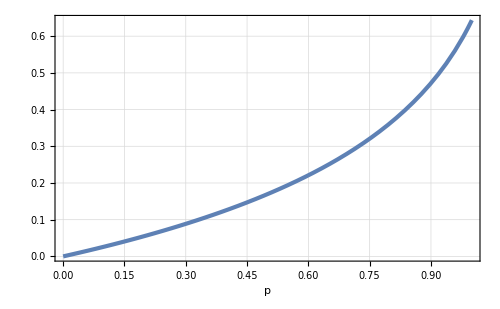

```mathematica
fig=Plot[
NSolve[exprKlyshko1[p,μ]==0&&μ>0,μ,Reals]⟦1,1,2⟧,
{p,0,1},PlotRange->All,
Frame->True,FrameStyle->Directive[Black,Thick,Large],GridLines->Automatic,PlotStyle->Thickness@0.006,PlotRangePadding->None,ImageSize->500,
FrameLabel->{"p"}
]
(*exportHere["blablabla.pdf",fig]*)
```

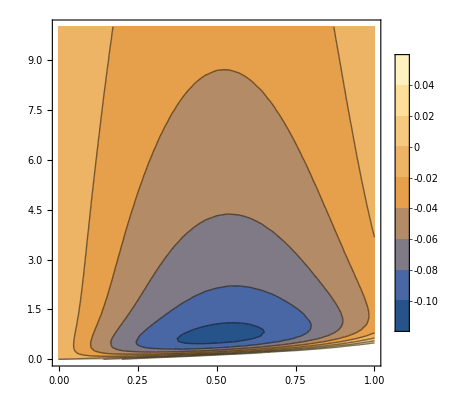

```mathematica
ContourPlot[
exprKlyshko1[p,μ],
{p,0,1},{μ,0,10},PlotLegends->Automatic
]
```

```mathematica
Reduce[exprKlyshko1[p,μ]≥0&&μ≥0,μ]//FullSimplify
```

(p==1&&0≤μ≤√(-1+√2))||(0<p<1&&0≤μ≤Root[p+(-4+4 p) #1+(-8+6 p) #1^2+(-6+6 p) #1^3+(-4+3 p) #1^4+(-2+2 p) #1^5&,3])||(1<p<Root[-13824+47232 #1-64132 #1^2+45417 #1^3-20060 #1^4+7102 #1^5-2040 #1^6+289 #1^7&,1]&&(0≤μ≤Root[p+(-4+4 p) #1+(-8+6 p) #1^2+(-6+6 p) #1^3+(-4+3 p) #1^4+(-2+2 p) #1^5&,2]||μ≥Root[p+(-4+4 p) #1+(-8+6 p) #1^2+(-6+6 p) #1^3+(-4+3 p) #1^4+(-2+2 p) #1^5&,3]))||(μ≥0&&(p+Root[13824+47232 #1+64132 #1^2+45417 #1^3+20060 #1^4+7102 #1^5+2040 #1^6+289 #1^7&,1]≥0||p≤0))